```mathematica
g=FinancialData["DAX","1.1.1980"];
```

```mathematica
g[[1]]
```

{{2000,1,3},6750.76}

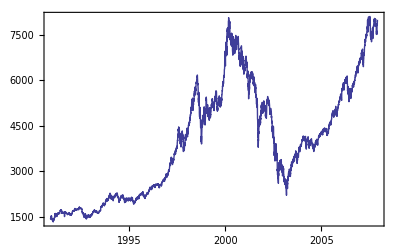

```mathematica
DateListPlot[g,Joined->True]
```

```mathematica
#[[2]]&/@{{a,2},{b,3},{c,4}}
```

{2,3,4}

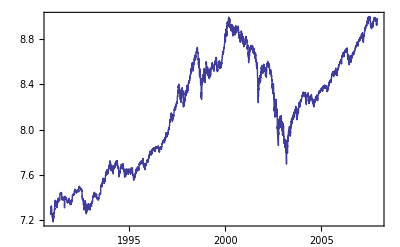

```mathematica
DateListPlot[{#[[1]],Log[#[[2]]]}&/@g,Joined->True]
```

```mathematica
m=Mean[Transpose[g][[2]]];o=Variance[Transpose[g][[2]]];
```

```mathematica
l=Length[g]
```

4300

```mathematica
c[t_]:=(Sum[g[[k,2]] g[[k+t,2]],{k,1,l-t}]/(l-t)-m^2)/l*(l+1)/o
```

```mathematica
c[0]
```

1.

```mathematica
ct=Table[c[t],{t,0,l-1}];
```

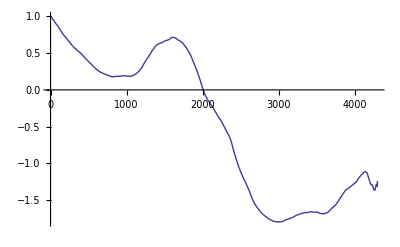

```mathematica
ListPlot[ct,Joined->True]
```

```mathematica
ca[t_,n_,s_]:=(Sum[g[[k,2]] g[[k+t,2]],{k,s,s+n-1-t}]/(n-t)-(Mean[g[[s;;s+n-1,2]]])^2)/l*(l+1)/Variance[g[[s;;s+n-1,2]]]
```

```mathematica
ca[3,l,1]
```

0.995807

```mathematica
c[3]
```

0.995807

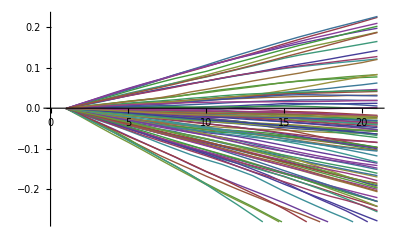

```mathematica
ListPlot[Table[Table[Log[ca[t,1000,20k]],{t,0,20}],{k,1,100}],Joined->True]
```